## 衰变规律

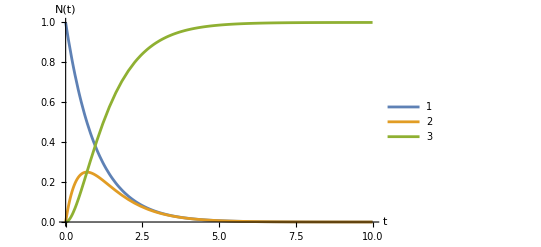

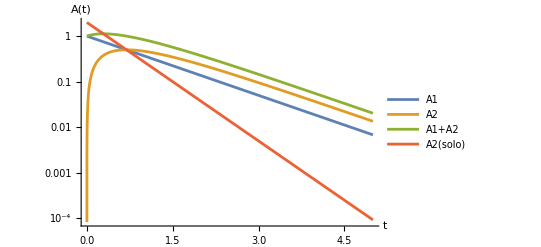

```mathematica
Clear["Global`*"]  
{λA=1,λB=2};
nA0=1;
T=10;
eqns ={nA'[t]==-λA nA[t],nB'[t]==λA nA[t]-λB nB[t],nC'[t]==λB nB[t],nA[0]==nA0,nB[0]==0,nC[0]==0} ;
sol=DSolve[eqns,{nA[t],nB[t],nC[t]},t];
Plot[Evaluate[{nA[t],nB[t],nC[t]}/. sol],{t,0,T},PlotLegends->{"1","2","3"},AxesLabel->{"t","N(t)"}]
LogPlot[Evaluate[{λA nA[t],λB nB[t],λA nA[t]+λB nB[t],λB Exp[-λB t]}/. sol],{t,0,0.5T},PlotLegends->{"A1","A2","A1+A2","A2(solo)"},AxesLabel->{"t","A(t)"}]
```

## 液滴模型

{337.272,1806.08}

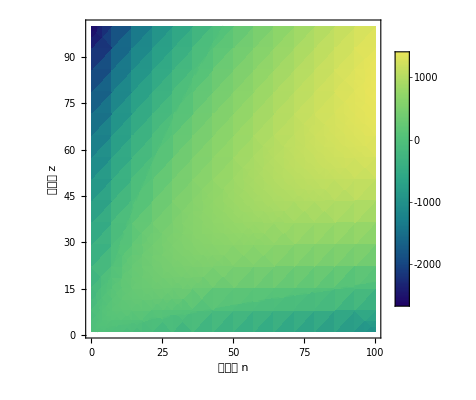

```mathematica
B[n_,Z_]:=15.835(Z+n)-18.330(Z+n)^(2/3)-0.7140 Z^2(Z+n)^(-1/3)-92.800((Z+n)/2-Z)^2(Z+n)^-1+11.2(Z+n)^(-1/2) Piecewise[{{1,EvenQ[Round[n]]&&EvenQ[Round[Z]]},{0,(-1)^(Round[Z]+Round[n])<0},{-1,OddQ[Round[n]]&&OddQ[Round[Z]]}}]
num=100;

{B[20,20],B[238-92,92]}(*Binding energy of ^40 Ca ^238 U *)

DensityPlot[B[n,Z],{n,0,num},{Z,1,num},ColorFunction->"BlueGreenYellow",MeshFunctions->{#3&},MeshStyle->Directive[Dashed,Thickness[Medium]],Mesh->{{0}},ClippingStyle->Automatic,PlotLegends->Automatic,FrameLabel->{"中子数 n","质子数 z"}]
```

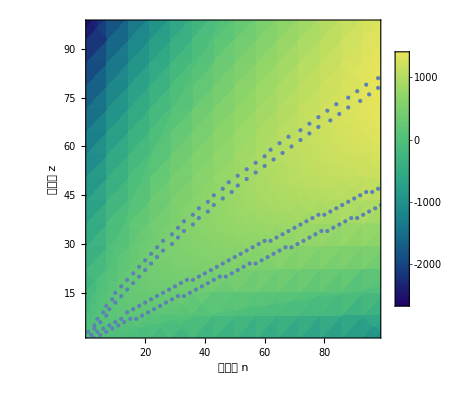

```mathematica
npoints=Flatten[Table[{n,Z},{n,0,num},{Z,1,num}],1];
validnPoints=Select[npoints,B[#[[1]],#[[2]]]>=B[#[[1]]+1,#[[2]]]&];
groupednPoints=GatherBy[validnPoints,First];
maxnPoints=Map[MaximalBy[#,Last]&,groupednPoints];
maxnPoints=Flatten[maxnPoints,1];

zpoints=Flatten[Table[{n,Z},{n,0,num},{Z,1,num}],1];
validzPoints=Select[zpoints,B[#[[1]],#[[2]]]>=B[#[[1]],#[[2]]+1]&];
groupedzPoints=GatherBy[validzPoints,Last];
maxzPoints=Map[MaximalBy[#,First]&,groupedzPoints];
maxzPoints=Flatten[maxzPoints,1];
Show[DensityPlot[B[n,Z],{n,0,num},{Z,1,num},ColorFunction->"BlueGreenYellow",MeshFunctions->{#3&},MeshStyle->Directive[Dashed,Thickness[Medium]],Mesh->{{0}},ClippingStyle->Automatic,PlotLegends->Automatic,FrameLabel->{"中子数 n","质子数 z"}],
ListPlot[maxnPoints,PlotStyle->{PointSize[Medium]},AxesLabel->{"n","Z"}],
ListPlot[maxzPoints,PlotStyle->{PointSize[Medium]},AxesLabel->{"n","Z"}],
PlotRange->{{2,num-3},{3,num-3}}
]
```

-Graphics-

### β 稳定线

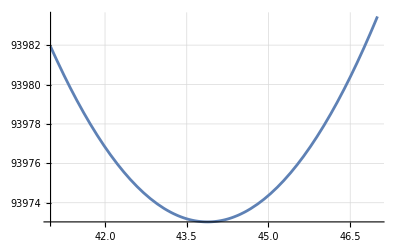

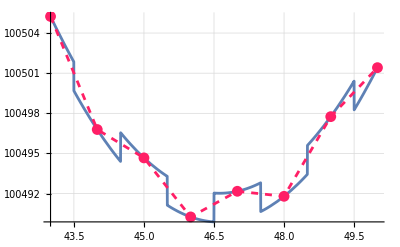

```mathematica
M[A_,Z_]:=938.2721 Z+939.5654(A-Z)-B[A-Z,Z];
Plot[M[101,Z],{Z,41,47},GridLines->Automatic]
Show[Plot[M[108,Z],{Z,43,50},GridLines->Automatic],
ListLinePlot[Table[{Z,M[108,Z]},{Z,43,50}],PlotStyle->{Dashed,RGBColor[1,0.12,0.4]},Mesh->All]
]
```

```mathematica
QuantityMagnitude[UnitConvert[Quantity[, "NeutronMass"] Quantity[, "SpeedOfLight"]^2,"MeV"]]
QuantityMagnitude[UnitConvert[Quantity[, "ProtonMass"] Quantity[, "SpeedOfLight"]^2,"MeV"]]
```

939.56542

938.272088

```mathematica
Entity["Isotope","Uranium238"][EntityProperty["Isotope","AtomicMass"]]
```

238.0508 u

```mathematica
QuantityMagnitude[UnitConvert[Quantity[238.050786936`7.871248293897896, "AtomicMassUnit"] Quantity[, "SpeedOfLight"]^2,"MeV"]]
```

221742.9

## 原子核物理思考题（带电体系相互作用）

```mathematica
Integrate[Exp[-β(x+I k/(2 β))^2],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√π)/(√β), Re[β]>0]

```mathematica
Integrate[Exp[a u],{u,-1,1}]
```

(2 Sinh[a])/a

```mathematica
Integrate[Exp[-v^2/(4β)](Exp[(R v)/(2 β)]-Exp[(-R v)/(2 β)]),{v,0,Infinity}]
```

2 ⅇ^(R^2/(4 β)) √π √β Erf[R/(2 √β)]

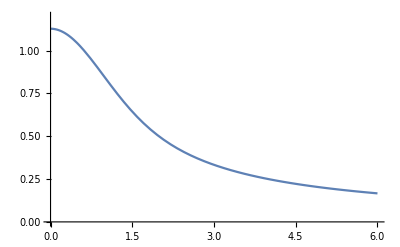

```mathematica
Plot[Erf[R]/R,{R,0,6},PlotRange->{{0,6},{0,1.2}}]
```

-(2 ⅇ^(-R^2))/(√π R)+Erf[R]/R^2

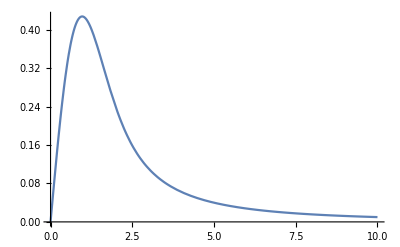

```mathematica
F[R_]:=-Erf[R]/R
F'[R]
Plot[F'[x],{x,0,10}]
```

```mathematica
Series[Erf[R]/R,{R,Infinity,1}]
```

ⅇ^(-R^2+O[1/R]^2) O[1/R]^2+(1/R+O[1/R]^2)

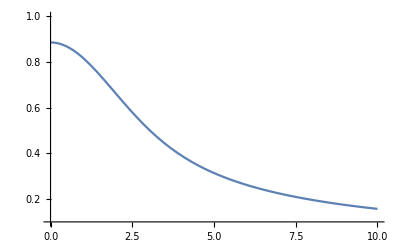

```mathematica
F[r_]:=NIntegrate[Exp[-k^2]Sinc[k r],{k,0,10}]
Plot[F[r],{r,0,10},PlotRange->{{0,10},{0.1,1}}]
```

```mathematica
Integrate[Sin[x]/(√(a^2+R^2+2 a R Cos[x])),{x,0,Pi}]
```

ConditionalExpression[4/(√((a-R)^2)+√((a+R)^2)), ]

```mathematica
Integrate[a/R(Exp[I k a]-Exp[-I k a]),{a,0,R}]+Integrate[(Exp[I k a]-Exp[-I k a]),{a,R,Infinity}]
```

ConditionalExpression[(2 ⅈ Cos[k R])/k+(2 ⅈ (-k R Cos[k R]+Sin[k R]))/(k^2 R), Im[k]<0&&Re[R]>0&&Im[R]==0]

```mathematica
UnitConvert[Quantity[, "ElectricConstant"],Quantity[, "ElementaryCharge"]^2/(Quantity[, "Megaelectronvolts"]*Quantity[, "Femtometers"])]
```

0.0552634936 e^2/(fm MeV)

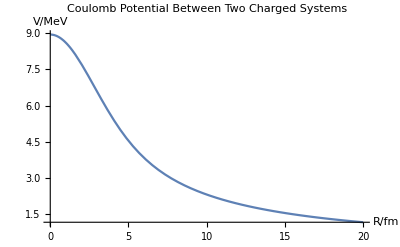

Potential at a distance of 10 fm =

2.30393 MeV

```mathematica
Subscript[α, 1]=0.123008;
Subscript[β, 1]=0.4895;
Subscript[α, 2]=0.088948;
Subscript[β, 2]=0.1565;
V[R_]:=((Subscript[α, 1] Subscript[α, 2]  Pi)/(2*0.05526349358057109578877651954261665007`9.532175381914792*(Subscript[β, 1] Subscript[β, 2])^(3/2)))NIntegrate[Exp[-(Subscript[β, 1]+Subscript[β, 2])/(4 Subscript[β, 1] Subscript[β, 2])k^2]Sinc[R k],{k,0,30}];
Plot[V[R],{R,0,20},AxesLabel->{"R/fm","V/MeV"},PlotLabel->"Coulomb Potential Between Two Charged Systems"]
Print["Potential at a distance of 10 fm ="]
V[10]Quantity[, "Megaelectronvolts"]
```

```mathematica
ClearAll
```

ClearAll

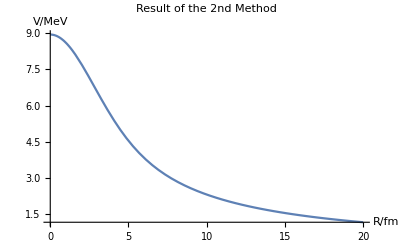

Potential at a distance of 10 fm =

2.30393 MeV

```mathematica
Subscript[α, 1]=0.123008;
Subscript[β, 1]=0.4895;
Subscript[α, 2]=0.088948;
Subscript[β, 2]=0.1565;
β=(Subscript[β, 1]+Subscript[β, 2])/(4 Subscript[β, 1] Subscript[β, 2]);
V[R_]:=(Pi^2  Subscript[α, 1] Subscript[α, 2])/(4 *0.05526349358057109578877651954261665007`9.532175381914792*(Subscript[β, 1] Subscript[β, 2])^(3/2))1/R Erf[R/(2 √β)];
Plot[V[R],{R,0,20},AxesLabel->{"R/fm","V/MeV"},PlotLabel->"Result of the 2nd Method"]
Print["Potential at a distance of 10 fm ="]
V[10]Quantity[, "Megaelectronvolts"]
```